# Correlation Sampling - Linewidth Process

## Last Updated: 2025/07/20

```mathematica
(*Quit[];*)
```

```mathematica
(*Remove["Global`*"];
ClearInOut[];*)
```

# General

## Values

## ARTIQ Conversions

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
ftwToFrequencyMHz=(1.*^-6)*(1.*^9)/(Interpreter["HexInteger"]["FFFFFFFF"]);
```

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
asfToAmplitudePCT=(1.*^2)*1./(Interpreter["HexInteger"]["3FFF"]);
```

## Fundamental

```mathematica
(*natural*)
ℏ=1.0545718*^-34;
c=2.99792458*^8;
```

```mathematica
(*statistical mechanics*)
kb=1.38064852*^-23;
```

```mathematica
(*electron units*)
me=9.10938356*^-31;
qe=1.60217662*^-19;
```

```mathematica
(*electromagnetism*)
ϵ0 = 8.8541878128*^-12;
μ0=π*4.*^-7;
```

```mathematica
(*atomic*)
amu=1.66053904*^-27;
```

## Derived

```mathematica
(*qe^2/(4 Subscript[πϵ, 0])*)
ke2=2.30707751*^-28;
```

```mathematica
(*fine structure constant*)
αfs=ke2/(ℏ*c);
```

```mathematica
(*bohr radius*)
a0=ℏ^2/(me*ke2);
```

```mathematica
(*bohr magneton*)
μB=(qe*ℏ)/(2*me);
```

```mathematica
(*debye*)
debye=(1.*^-21)/c;
```

## Units

```mathematica
(*frequency*)
{khz,mhz,ghz}={10.^3,10.^6,10.^9};
{wkhz,wmhz,wghz}=2.π*{10.^3,10.^6,10.^9};
```

```mathematica
(*time*)
{ns,μs,ms}={10.^-9,10.^-6,10.^-3};
```

```mathematica
(*distance*)
{nm,μm,mm}={10.^-9,10.^-6,10.^-3};
```

## Plotting

```mathematica
(*set plot options - analytical*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[LogPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set plot options - list*)
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set signal plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

## Evaluations

```mathematica
(*scde2={
Off[General::munfl],
Off[FindRoot::lstol],
Off[FindFit::cvmit],
Off[FindFit::sszero],
Off[FindFit::nrjnum],
Off[NonlinearModelFit::cvmit],
Off[NonlinearModelFit::sszero],
Off[Power::infy],
Off[Infinity::indet],
Off[FittedModel::constr]
};*)
```

```mathematica
(*Evaluate[#]&/@scde2*)
```

```mathematica
(*scde={
General::munfl,
FindRoot::lstol,
FindFit::cvmit,
FindFit::sszero,
FindFit::nrjnum,
NonlinearModelFit::cvmit,
NonlinearModelFit::sszero,
Power::infy,
Infinity::indet,
FittedModel::constr
};*)
```

```mathematica
(*Off[#]&/@scde*)
```

```mathematica
(*turn upsetting things off*)
ParallelEvaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
];
Evaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
];
```

## Functions

## Phonon Conversion

### Coherent_C

```mathematica
(*coherent_c: convert R/B ratio to <n> assuming a coherent state*)
```

```mathematica
coherentX0="0\t9.99968345065521e-05\t0.000399949359050543\t0.000899743688795304\t0.00159919018917467\t0.00249802373567682\t0.00359590407662662\t0.00489241629804741\t0.00638707138943964\t0.00807930690905264\t0.00996848774698177\t0.0120539069841832\t0.0143347868452619\t0.0168102797426638\t0.0194794694096749\t0.0223413721194334\t0.0253949379869404\t0.0286390523508750\t0.0320725372318338\t0.0356941528634366\t0.0395025992925868\t0.0434965180450157\t0.0476744938521131\t0.0520350564349007\t0.0565766823409077\t0.0612977968295938\t0.0661967758018701\t0.0712719477691913\t0.0765215958576296\t0.0819439598422616\t0.0875372382071775\t0.0932995902263676\t0.0992291380607130\t0.105323968866310\t0.111582136909319\t0.118001665682565\t0.124580550019086\t0.131316758197884\t0.138208234037120\t0.145252898970045\t0.152448654098991\t0.159793382222768\t0.167284949832890\t0.174921209074062\t0.182699999664427\t0.190619150771128\t0.198676482836768\t0.206869809352429\t0.215196938572920\t0.223655675170015\t0.232243821819463\t0.240959180717564\t0.249799555023207\t0.258762750221224\t0.267846575402984\t0.277048844460143\t0.286367377187489\t0.295800000290804\t0.305344548295672\t0.314998864353126\t0.324760800938008\t0.334628220435874\t0.344598995614207\t0.354671009973656\t0.364842157974930\t0.375110345136883\t0.385473488001222\t0.395929513959161\t0.406476360935198\t0.417111976923057\t0.427834319368674\t0.438641354394938\t0.449531055862707\t0.460501404262433\t0.471550385430509\t0.482675989084237\t0.493876207169105\t0.505149032011798\t0.516492454272143\t0.527904460686948\t0.539383031598436\t0.550926138259732\t0.562531739909640\t0.574197780608683\t0.585922185828196\t0.597702858784029\t0.609537676506275\t0.621424485636251\t0.633361097941900\t0.645345285542670\t0.657374775834950\t0.669447246109191\t0.681560317849959\t0.693711550710419\t0.705898436153020\t0.718118390748662\t0.730368749127130\t0.742646756572379\t0.754949561257081\t0.767274206112027\t0.779617620327223\t0.791976610483122";
coherentX0=Internal`StringToMReal/@StringSplit[coherentX0,"\t"];
```

```mathematica
coherentY0="0\t0.000100000000000000\t0.000400000000000000\t0.000900000000000000\t0.00160000000000000\t0.00250000000000000\t0.00360000000000000\t0.00490000000000000\t0.00640000000000000\t0.00810000000000000\t0.0100000000000000\t0.0121000000000000\t0.0144000000000000\t0.0169000000000000\t0.0196000000000000\t0.0225000000000000\t0.0256000000000000\t0.0289000000000000\t0.0324000000000000\t0.0361000000000000\t0.0400000000000000\t0.0441000000000000\t0.0484000000000000\t0.0529000000000000\t0.0576000000000000\t0.0625000000000000\t0.0676000000000000\t0.0729000000000000\t0.0784000000000000\t0.0841000000000000\t0.0900000000000000\t0.0961000000000000\t0.102400000000000\t0.108900000000000\t0.115600000000000\t0.122500000000000\t0.129600000000000\t0.136900000000000\t0.144400000000000\t0.152100000000000\t0.160000000000000\t0.168100000000000\t0.176400000000000\t0.184900000000000\t0.193600000000000\t0.202500000000000\t0.211600000000000\t0.220900000000000\t0.230400000000000\t0.240100000000000\t0.250000000000000\t0.260100000000000\t0.270400000000000\t0.280900000000000\t0.291600000000000\t0.302500000000000\t0.313600000000000\t0.324900000000000\t0.336400000000000\t0.348100000000000\t0.360000000000000\t0.372100000000000\t0.384400000000000\t0.396900000000000\t0.409600000000000\t0.422500000000000\t0.435600000000000\t0.448900000000000\t0.462400000000000\t0.476100000000000\t0.490000000000000\t0.504100000000000\t0.518400000000000\t0.532900000000000\t0.547600000000000\t0.562500000000000\t0.577600000000000\t0.592900000000000\t0.608400000000000\t0.624100000000000\t0.640000000000000\t0.656100000000000\t0.672400000000000\t0.688900000000000\t0.705600000000000\t0.722500000000000\t0.739600000000000\t0.756900000000000\t0.774400000000000\t0.792100000000000\t0.810000000000000\t0.828100000000000\t0.846400000000000\t0.864900000000000\t0.883600000000000\t0.902500000000000\t0.921600000000000\t0.940900000000000\t0.960400000000000\t0.980100000000000\t1\t1.02010000000000";
coherentY0=Internal`StringToMReal/@StringSplit[coherentY0,"\t"];
```

```mathematica
(*CoherentC=Interpolation[Transpose[{coherentX0,coherentY0}]];*)
CoherentCFunc=Interpolation[Transpose[{coherentX0,coherentY0}]];
CoherentC[x_]:=CoherentCFunc[#]&[Clip[x,{0.,0.8}]];
```

### Coherent_R

```mathematica
(*coherent_c: convert RSB probability ONLY to <n> assuming a coherent state*)
```

```mathematica
coherentR0={
0,9.99931658497433*^-5,0.000399890663733249,0.000899446570690410,0.00159825126849689,0.00249573182347329,0.00359115251770981,0.00488361553119066,0.00637206177417027,0.00805527186899924,0.00993186728045770,0.0120003115935124,0.0142589119372707,0.0167058205537671,0.0193390365100727,0.0221564075520917,0.0251556320982592,0.0283342613712326,0.0316897016655309,0.0352192167489441,0.0389199303954148,0.0427888290469539,0.0468227646020514,0.0510184573278918,0.0553724988935951,0.0598813555215709,0.0645413712539629,0.0693487713310517,0.0742996656783876,0.0793900524992962,0.0846158219693280,0.0899727600291077,0.0954565522719444,0.101062787922491,0.106786963902628,0.112624488980697,0.118570688000088,0.124620806183157,0.130770013506336,0.137013409142264,0.143346025964675,0.149762835111746,0.156258750603538,0.162828634009109,0.169467299158846,0.176169516897511,0.182930019873458,0.189743507359448,0.196604650100454,0.203508095183842,0.210448470927264,0.217420391779606,0.224418463230326,0.231437286722481,0.238471464564783,0.245515604837990,0.252564326290965,0.259612263221736,0.266654070338924,0.273684427598902,0.280698045014097,0.287689667427855,0.294654079251349,0.301586109158018,0.308480634731091,0.315332587059793,0.322136955279870,0.328888791054132,0.335583212988793,0.342215410981400,0.348780650496278,0.355274276763424,0.361691718896910,0.368028493928910,0.374280210755539,0.380442573990817,0.386511387725119,0.392482559184592,0.398352102288109,0.404116141098438,0.409770913164383,0.415312772750811,0.420738193953524,0.426043773696107,0.431226234605960,0.436282427766861,0.441209335345508,0.446004073089648,0.450663892695473,0.455186184042142,0.459568477291385,0.463808444850291,0.467903903195516,0.471852814557270,0.475653288461590,0.479303583129547,0.482802106732168,0.486147418499979,0.489338229686260,0.492373404383192,0.495251960190268,0.497973068734440,0.500536056041652,0.502940402759546,0.505185744231242,0.507271870420298,0.509198725687029,0.510966408416576,0.512575170499202,0.514025416663485,0.515317703663170,0.516452739318639,0.517431381414049,0.518254636451358,0.518923658262584,0.519439746481792,0.519804344878417,0.520019039553689,0.520085557002049,0.520005762039560,0.519781655601477,0.519415372411236,0.518909178523259,0.518265468742100,0.517486763920557,0.516575708139507,0.515535065772334,0.514367718436921,0.513076661838286,0.511665002505056,0.510135954423077,0.508492835569525,0.506739064351023,0.504878155949329,0.502913718578252,0.500849449655556,0.498689131893661,0.496436629313061,0.494095883182420,0.491670907889407,0.489165786746364,0.486584667734993,0.483931759194270,0.481211325455891,0.478427682431564,0.475585193156511,0.472688263293616,0.469741336602651,0.466748890379059,0.463715430866808,0.460645488649837,0.457543614026645,0.454414372372584,0.451262339494410,0.448092096981688,0.444908227559604,0.441715310447763,0.438517916729525,0.435320604736432,0.432127915452247,0.428944367941117,0.425774454804329,0.422622637670119,0.419493342720928,0.416390956262505,0.413319820339149,0.410284228399400,0.407288421016389,0.404336581667029,0.401432832574140,0.398581230615570,0.395785763304283,0.393050344843310,0.390378812259402,0.387774921619125,0.385242344331059,0.382784663537692,0.380405370600468,0.378107861681413,0.375895434424601,0.373771284740682,0.371738503697539,0.369800074520074,0.367958869701985,0.366217648232303,0.364579052939329,0.363045607954507,0.361619716298632,0.360303657592692,0.359099585895489,0.358009527670097,0.357035379881037,0.356178908223974,0.355441745489547,0.354825390062886,0.354331204560147,0.353960414603333,0.353714107734502,0.353593232470306,0.353598597497709,0.353730871011554};
```

```mathematica
coherentRX0=Range[0.,2.,2./(Length[coherentR0]-1)]^2.;
```

```mathematica
(*note: need to truncate after 120 points b/c curve is non-injective after that*)
CoherentRFunc=Interpolation[Transpose[{coherentR0,coherentRX0}][[;;120]]];
CoherentR[x_]:=CoherentRFunc[#]&[Clip[x,{0.,0.6}]];
```

### Coherent_ARP

```mathematica
(*todo: account for n != 0*)
CoherentARP[P_,n_:0]:=-Log[P+1.*^-7];
```

## Dataset Processing

### Import

```mathematica
(*import dataset from dir and filename, return dataset and parameters*)
ImportDatasetARTIQ[filedirs_:(_String|_List),ridName:(_String|_Integer)]:=Module[
{
filenameDJ,
fileDirectories=filedirs,

(*dataset values*)
datasetRaw,
parameterList
},

(*ensure filedirs is a list*)
If[Head[fileDirectories]==String,
fileDirectories={filedirs}
];

(*ensure import directory exists*)
If[!AnyTrue[DirectoryQ/@filedirs],

(*stop execution if import directory doesn't exist*)
MessageDialog["Failure :(\nError: Import directory not found."];
FrontEndTokenExecute["EvaluatorAbort"];
];


filenameDJ=FileNames["*"<>ToString[#]<>"*.h5",filedirs,Infinity]&[ridName];

(*stop execution if file doesn't exist*)
If[Length[filenameDJ]==0,

MessageDialog["Failure :(\nError: Specified file not found ("<>ToString[ridName]<>")."];
FrontEndTokenExecute["EvaluatorAbort"],

filenameDJ=First@filenameDJ;
];

(*extract file results as list and parameters as an association*)
datasetRaw=Import[filenameDJ,{"/datasets/results"}];
parameterList=Join@@{
Import[filenameDJ,{"Attributes","/arguments"}],
Import[filenameDJ,{"Attributes","/parameters"}]
};

Return[{datasetRaw,parameterList}];
];
```

### Processing

```mathematica
(*threshold counts into s-state vs d-state probability*)
Options[ThresholdCounts]={
"Threshold"->-1
};
ThresholdCounts[dataset_List,countsColumn_Integer,OptionsPattern[]]:=Module[
{
results=dataset,

(*find state discrimination threshold*)
countThreshold=If[
OptionValue["Threshold"]!=-1,
OptionValue["Threshold"],
FindThreshold[dataset[[;;,countsColumn]],Method->"MinimumError"]
]
},

(*directly threshold counts into D-state probability*)
results[[;;,countsColumn]]=1.-UnitStep[results[[;;,countsColumn]]-countThreshold];
(*Print[countThreshold];*)
Return[results];
];
```

```mathematica
(*group the data as desired, then take the mean of whatever remains*)
CollateData[dataset_List,groupColumnList_List]:=GroupBy[dataset,
Table[
With[{i=i},#[[i]]&],
{i,groupColumnList}
],
N[Mean[#]]&
]//KeySort;
```

### Analysis

```mathematica
(*sinc-squared function for spetroscopy fitting*)
SincModel[α_,β_,δ_,t_,x_]:=α*Sinc[(π*t)*((x-β)*khz)+0.0000000001]^2+δ;
```

```mathematica
(*fit sinc and return params with error and confidence intervals*)
FitSinc[dataset_List,timeSinc:(_Integer|_Real)]:=Module[
{
guessMax=dataset[[First@Ordering[dataset[[;;,2]],-1]]],
guessOffset=Mean[{Median[dataset[[;;,2]]],Mean[dataset[[;;,2]]]}],
guessParamList,

α,β,γ,δ,x,
sincConstraints,
sincModel,

fitResult
},

(*create sinc model*)
sincModel=α*Sinc[(π*timeSinc)*((x-β)*khz)+0.00000001]^2+δ;

(*guess sinc fit parameters*)
guessParamList={
(guessMax[[2]]-guessOffset),(*rabi frequency*)
guessMax[[1]],(*resonance frequency*)
guessOffset (*background offset*)
};

(*constrain search range for parameters*)
sincConstraints={
(*α>0,α<αRSBguess*3,*)
(*β>0.975*βRSBguess,β<1.025*βRSBguess*)
δ>0
};

(*fit sinc model - nonlinearmodelfit to extract extra fit information*)
fitResult=NonlinearModelFit[
dataset,
Join[{sincModel,sincConstraints}],
Transpose[{{α,β,δ},guessParamList}],
x,
MaxIterations->10^4
];

(*todo: return parameters and their error*)
Return[fitResult["ParameterConfidenceIntervalTableEntries"]];
];
```

# User Input

```mathematica
(*top level directory for imports*)
(*directoryString="Z:\\motion\\Data\\2025-07\\2025-07-12";*)
directoryString="Z:\\motion\\Data\\2025-09\\2025-09-";
(*directoryString="/Volumes/groups/motion/Data/2025-04/2025-04-08";*)
```

```mathematica
(*general config*)
rid=121089;
timeCol=1;(*timestamp column*)
countCol=2;(*raw count column*)
```

```mathematica
(*specific config*)
procStyle="RAP";(*sideband ratio: "SBR", 729: "729"*)
```

## Validate User Input

```mathematica
(*check input directory exists*)
If[!DirectoryQ[directoryString],
MessageDialog["Failure :(\nError: Import directory not found ("<>directoryString<>")."];
FrontEndTokenExecute["EvaluatorAbort"];
];
```

# Import & Process (Initial)

## Import Dataset

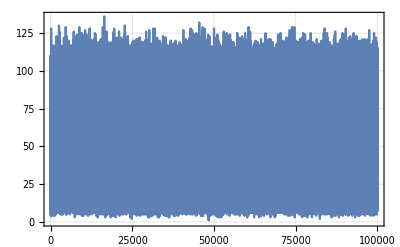
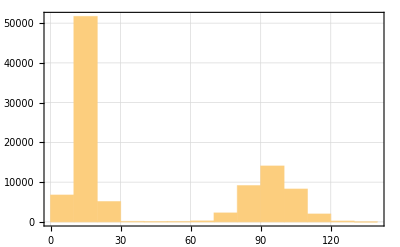
{(6.27194×10^14 | 11. | 6.27194×10^14
6.27194×10^14 | 9. | 6.27194×10^14
6.27194×10^14 | 12. | 6.27194×10^14),-Graphics-,-Graphics-}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
dataset[[;;3,;;]]//MatrixForm,
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]]
}&[dataset[[;;,2]]]
{
(*parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"]*)
};
```

## Preprocess

```mathematica
(*threshold counts & convert units*)
datasetProcessed=ThresholdCounts[dataset[[;;,{timeCol,countCol}]],2];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ns,1.}];
```

```mathematica
(*subtract initial time*)
datasetProcessed[[;;,1]]-=datasetProcessed[[1,1]];
(*separate out values for convenience*)
dataSampledArr=datasetProcessed[[;;,2]];
tmax=datasetProcessed[[-1,1]]-datasetProcessed[[1,1]];
```

## FFT - Do

```mathematica
(*guess fmax by averaged sample period*)
numSamplePoints=Length[datasetProcessed];
fmax=1./Mean[datasetProcessed[[2;;,1]]-datasetProcessed[[1;;-2,1]]];
(*calculate x-axis for FFT (i.e. freqs)*)
dataFFTFreqs=Range[0,fmax/2.,fmax/(numSamplePoints-1)][[;;IntegerPart[numSamplePoints/2.]]];
```

```mathematica
(*apply FFT to sampled measurements (w/DC subtraction)*)
AbsoluteTiming[
dataFFTFull=Fourier[
dataSampledArr-Mean[dataSampledArr],
FourierParameters->{1,-1}
];
]
(*set correct FFT length*)
dataFFTChop=dataFFTFull[[;;IntegerPart[numSamplePoints/2.]]];
```

{0.0016914,Null}

```mathematica
(*format results for display*)
dataFFTMag=Transpose[{
dataFFTFreqs,
Abs[dataFFTChop]^2.
}];
dataFFTPhase=Transpose[{
dataFFTFreqs,
1./π*Arg[dataFFTChop]
}];
```

## FFT - Plot

```mathematica
(*plot FFT'd data*)
plotDataFFTMag=ListPlot[
{
dataFFTMag
(*fftSampledPeakCallouts*)
},
Joined->{
True,False
},
PlotRange->{
{Full,Full},
{Full,Full}
},
PlotRangePadding->False,

FrameLabel->{
 {Style["Power (Ampl^2)",{Black,Directive[15]}],None},
{
Style["Frequency (Hz)",{Black,Directive[15]}],
Style["CorrSamp FFT (RID: "<>ToString[rid]<>")",{Black,Directive[15]}]
}
},
ImageSize->Scaled[0.45],
PerformanceGoal->"Speed"
];
```

## Fit Lorentzian!

```mathematica
(*fit function*)
fitfunc=A/(Γ^2.+(x-f)^2.);
fitConstraintsDJ={(*A>0.,Γ>0.*)};
peakIndDJ=Ordering[dataFFTMag[[;;,2]],-1];
fitGuessDJ={
{A,1.*Abs[Subtract@@MinMax[dataFFTMag[[;;,2]]]]*(0.25/tmax)^2.},
{Γ,0.25/tmax},
{f,1.*First@dataFFTMag[[peakIndDJ,1]]}
}
```

{{A,5.38838},{Γ,0.000227275},{f,10.0001}}

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
dataFFTMag,
Join[{fitfunc},fitConstraintsDJ],
fitGuessDJ,
x
];
]
```

{0.485287,Null}

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Show

| Estimate | Standard Error | Confidence Interval
A | 0.615974 | 0.117205 | {0.386252,0.845697}
Γ | 0.0000556655 | 0.00008492 | {-0.000110779,0.00022211}
f | 10. | 0.0000852378 | {9.99988,10.0002}

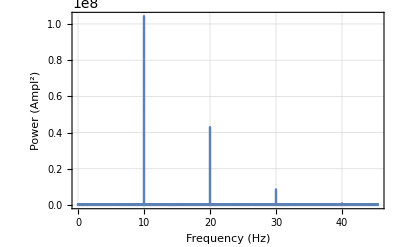

```mathematica
fitParams
plotDataFFTMag
```

# Precision (95% conf.int.) vs # Points Used for Fit

```mathematica
(*create x-axis array of # of points to scan*)
(*pointsArrX=Join[
Range[2,10],
Range[10,250,5],
Range[200,10000,25],
Range[10000,Length[dataFFTMag]/2,150]
]//IntegerPart//DeleteDuplicates//Sort;*)
pointsArrX=Join[
Range[2,10],
Range[10,250,5],
Range[200,1000,25]
]//IntegerPart//DeleteDuplicates//Sort;
Length[pointsArrX]
```

87

## Prepare

```mathematica
(*create func to fit lorentzian to subranges of known dataset*)
Clear[FitSweepFunc];
FitSweepFunc[subRange_]:=With[
{
dataFFTFitTMP=dataFFTMag[[
Max[1,peakIndDJ-subRange];;
Min[Length[dataFFTMag],peakIndDJ+subRange]
]]
},
Return[
{
(*x-axis value: # of points*)
Length[dataFFTFitTMP],

(*result: fit result*)
NonlinearModelFit[
dataFFTFitTMP,
Join[{fitfunc},fitConstraintsDJ],
fitGuessDJ,
x
]
}
];
];
```

## Do & Plot

```mathematica
(*fit subarrays!*)
AbsoluteTiming[
fitResArrY=ParallelMap[
FitSweepFunc,
pointsArrX
];
]
```

{0.0886349,Null}

```mathematica
(*extract confidence intervals from fit results*)
AbsoluteTiming[
fitConfIntY=ParallelMap[
#["ParameterConfidenceIntervals"]&,
fitResArrY[[;;,2]]
];
]
(*format for plotting*)
subRangeFitData=Transpose[{fitResArrY[[;;,1]],Abs[Subtract@@@fitConfIntY[[;;,3]]]}];
```

{0.354275,Null}

```mathematica
(*plot confidence intervals*)
subRangeFitPlot=ListLogLogPlot[
{
subRangeFitData,subRangeFitData
},

PlotRange->{
{Full,Full},
{Full,Full}
},
FrameLabel->{ 
{Style["Conf. Int. (95%, Hz)",{Black,Directive[15]}],None},
{
Style["# of Points",{Black,Directive[15]}],
Style["Effect of Sample Number on Precision\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},

Joined->{True,False},
ImageSize->Scaled[0.6]
];
```

```mathematica
(*get some params for fun*)
subRangeFitParams=Style[
#["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
]&/@fitResArrY[[;;10,2]];
```

## Show

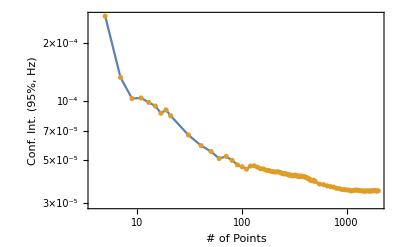

```mathematica
subRangeFitPlot
```

## Verify Fits Generally OK

```mathematica
scde0={1,20,-1};
scde1=fitResArrY[[scde0,1]]
```

{5,131,2001}

```mathematica
xranges={peakIndDJ[[1]]-20,peakIndDJ[[1]]+20};
xrangesFreq=dataFFTMag[[xranges,1]];
yPoints=dataFFTMag[[xranges[[1]];;xranges[[2]]]];
```

```mathematica
zz0=ListPlot[
{yPoints},
Joined->{False},
PlotRange->Full
];
zz1=Plot[
#,
{x,xrangesFreq[[1]],xrangesFreq[[2]]},

PlotRange->Full,
PlotLegends->scde1
]&[#[x]&/@fitResArrY[[scde0,2]]];
```

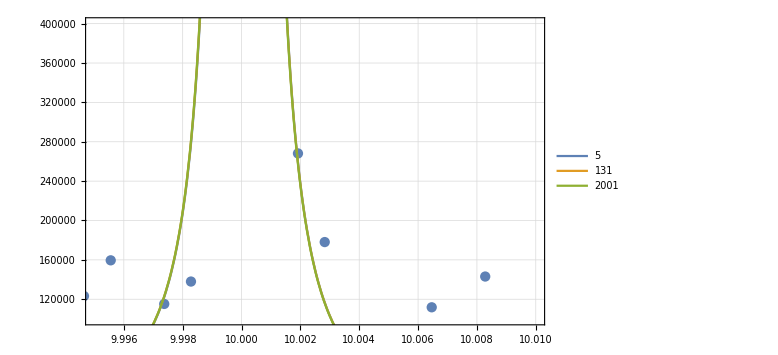

```mathematica
Show[
{zz0,zz1},
PlotRange->{
{9.995,10.010},
{1.*^5,4.*^5}
}
(*PlotRange->Full*)
]
```

# Quasi-ADEV of Resolution/Uncertainty vs Samples/Time

```mathematica
(*datasetProcessed=datasetProcessed[[248200;;]];*)
```

```mathematica
(*number of points to use for sweep*)
(*todo: implement*)
fitDataLength=100;
```

```mathematica
(*create x-axis array of # of points to use for FFT*)
sampleLengthArrX=Join[
Range[100,100,5],
Range[100,1000,20],
Range[1000,10000,100],
Range[10000,100000,500]
]//IntegerPart//DeleteDuplicates//Sort;
Length[sampleLengthArrX]
```

316

## Process Functions

## FFT Fit

```mathematica
(*direct process & fit FFT*)
Clear[FFTBlockFit];
FFTBlockFit[data_]:=Module[
{
(*helper variables*)
numSamplePoints=Length[data],
tmax=data[[-1,1]]-data[[1,1]],
fmax=1./Mean[data[[2;;,1]]-data[[1;;-2,1]]],

(*fft-related*)
dataFFTMag,

(*lorentzian fitting*)
peakIndDJ,fitRes,

(*tmptmp*)
peakIndDJ1,peakIndDJ2
},

(*do FFT*)
dataFFTMag=Transpose[{
(*fft freqs - x-axis*)
Range[0,fmax/2.,fmax/(numSamplePoints-1)][[;;IntegerPart[numSamplePoints/2.]]],

(*fft values - power (i.e. ampl^2)*)
Abs[
Fourier[
data[[;;,2]]-Mean[data[[;;,2]]],
FourierParameters->{1,-1}
][[;;IntegerPart[numSamplePoints/2.]]]
]^2.
}];


(*prepare fitting, then do fit*)
peakIndDJ=First@Ordering[dataFFTMag[[;;,2]],-1];
(*Print[peakIndDJ];
Print[dataFFTMag[[peakIndDJ]]];
Print[Dimensions[dataFFTMag]];*)

(*do fit*)
fitRes=NonlinearModelFit[
(*raw data*)
dataFFTMag,(*full*)
(*dataFFTMag[[2;;IntegerPart[2*peakIndDJ-2],;;]],(*only until 2nd harmonic*)*)
(*dataFFTMag[[peakIndDJ-2;;peakIndDJ+2,;;]],(*3-ish points only*)*)

(*fit function*)
{A/(Γ^2.+(x-f)^2.)},

(*fit guesses*)
{{A,1.*Abs[Subtract@@MinMax[dataFFTMag[[;;,2]]]]*(0.25/tmax)^2.},
{Γ,0.25/tmax},
{f,1.*dataFFTMag[[peakIndDJ,1]]}},
x
];

Return[fitRes];
];
```

## ADEV Linear Fitting

```mathematica
(*fit function*)
FitPowerFunc[dataset_]:=Block[{
A,x,K,B,
guessK,guessA,
logData=Log[dataset]
},

guessK=Mean[(#[[;;,2]])/(#[[;;,1]])]&[logData[[2;;]]-logData[[;;-2]]];
guessA=Exp[Mean[logData[[;;,2]]-guessK*logData[[;;,1]]]];

Return[
NonlinearModelFit[dataset,
{A*x^K},
{{A,guessA},
{K,guessK}},
x
]
];
];
```

```mathematica
(*fit function*)
FitLinearFunc[dataset_]:=Block[{
x
},

Return[
LinearModelFit[Log[dataset],
{x},
x
]
];
];
```

## Do Process

## Raw Data Batch Fit

```mathematica
(*convert indices/# of points to total measurement time*)
sampleTimeArrX=datasetProcessed[[sampleLengthArrX,1]];
```

```mathematica
(*process constituent FFTs*)
AbsoluteTiming[
ADEVFitRes=ParallelMap[
FFTBlockFit[datasetProcessed[[;;#]]]&,
sampleLengthArrX
];
]
```

{7.19861,Null}

```mathematica
(*precision: extract confidence intervals from fit results for plotting*)
AbsoluteTiming[
precisionADEVData=ParallelMap[
#["ParameterConfidenceIntervals"][[3]]&,
ADEVFitRes
];
(*format precisions for plotting*)
precisionADEVData=Transpose[{
sampleTimeArrX,
Abs[Subtract@@@precisionADEVData]}
];
]
```

{29.4681,Null}

```mathematica
(*resolution: extract confidence intervals from fit results for plotting*)
AbsoluteTiming[
resolutionADEVData=ParallelMap[
Γ/.#["BestFitParameters"]&,
ADEVFitRes
];
(*format precisions for plotting*)
resolutionADEVData=Transpose[{
sampleTimeArrX,
Abs[Subtract@@@resolutionADEVData]
}];
]
```

{24.7143,Null}

## Fit ADEV Lines & Plot

```mathematica
(*do power fits to normal data*)
th0=FitPowerFunc/@{precisionADEVData,resolutionADEVData};
th1=LogLogPlot[
#[x],
{x,#["Data"][[1,1]],#["Data"][[-1,1]]},
FrameLabel->{ 
{Style["Frequency (Hz)",{Black,Directive[15]}],None},
{
Style["Meausurement Time (s)",{Black,Directive[15]}],
Style["Parameter Scaling\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
}
]&/@th0;
th2=Style[
#["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
]&/@th0;
```

```mathematica
(*do linear fits to log'd data*)
sc0=FitLinearFunc/@{precisionADEVData,resolutionADEVData};
sc1=LogLogPlot[
Exp[#[Log[x]]],
{x,Exp[#["Data"][[1,1]]],Exp[#["Data"][[-1,1]]]},

FrameLabel->{ 
{Style["Frequency (Hz)",{Black,Directive[15]}],None},
{
Style["Meausurement Time (s)",{Black,Directive[15]}],
Style["Parameter Scaling\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
}
]&/@sc0;
sc2=Style[
#["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
]&/@sc0;
```

## Plot Results

```mathematica
1/x0 Integrate[x^2*Sin[x]^4,{x,0,x0}]//FullSimplify//Expand
```

x0^2/8-1/4 Cos[2 x0]+1/64 Cos[4 x0]+Sin[2 x0]/(8 x0)-1/4 x0 Sin[2 x0]+1/16 x0 Cos[2 x0] Sin[2 x0]-Sin[4 x0]/(256 x0)

```mathematica
(*plot confidence intervals*)
precisionADEVDataPlot=ListLogLogPlot[
{
precisionADEVData,precisionADEVData(*precision*)
(*resolutionADEVData,resolutionADEVData(*resolution*)*)
},

PlotRange->{
{Full,Full},
{Full,Full}
},

(*plot formatting*)
PlotRangePadding->False,
FrameTicksStyle->Directive[Black,20],
FrameLabel->{ 
{Style["Conf. Int. (95%, Hz)",{Black,Directive[15]}],None},
{
Style["Meausurement Time (s)",{Black,Directive[15]}],
Style["Parameter Scaling\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},

(*labelling*)
PlotLabels->Placed[
{
"Precision",None,
"Resolution",None
},
{{Scaled[0.7],Before}}
],

(*size output image*)
Joined->{True,False},
AspectRatio->Full,
ImageSize->{800,500}
];
```

## Show

{ | Estimate | Standard Error | Confidence Interval
1 | 0.790805 | 0.107168 | {0.579947,1.00166}
x | -1.19586 | 0.0204057 | {-1.23601,-1.15571}}

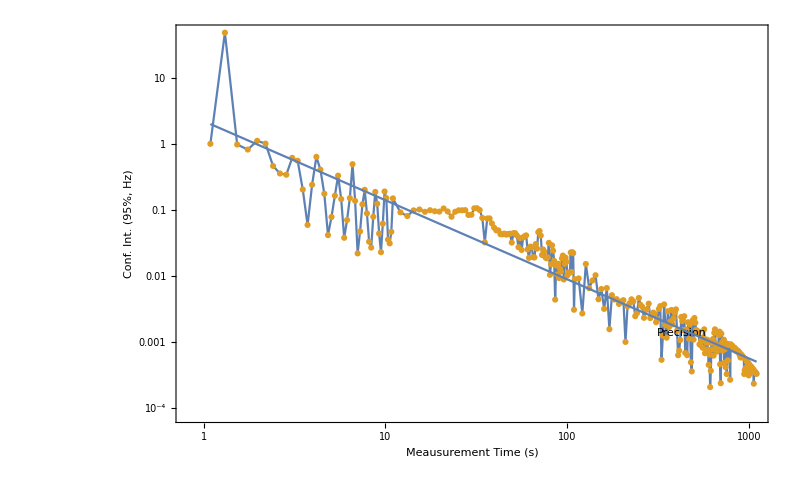

```mathematica
{(*th2[[1]],*)sc2[[1]]}
Show[
{precisionADEVDataPlot,(*th1[[1]],*)sc1[[1]]}
]
```

# Deprecated

```mathematica
(*Options[Plot2DResults]={
(*{{title_label},{x_label},{y_label}}*)
"AxesLabels"->{{""},{""},{""}},
"ImageSize"->Scaled[0.35],
"args"->None
};
(*Plot2DResults[data_List,args___:None,OptionsPattern[]]:=Block[*)
Plot2DResults[data_List,OptionsPattern[{Options[Plot2DResults],ListDensityPlot}]]:=Block[
{
AxesLabelVals=OptionValue["AxesLabels"]
},
Return[];
];*)
```

```mathematica
(*(*plot fitted results*)
fitPlot=
Plot[
fitRes[ϕ],
{ϕ,dsN[[1,1]],dsN[[-1,1]]}
];*)
```

```mathematica
(*summaryFigure={
(*processed data*)
Show[
ListPlot[
{
dsN
},
PlotRange->{
{Automatic,Automatic},
{0.,1.}
},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{
Style["Phase (turns)",{Black,Directive[15]}],
Style["Phase Sweep ("<>procStyle<>") - RID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{Black},
ImageSize->Scaled[0.45]
],
fitPlot
],
(*probability data*)
ListPlot[
dsRawPlot,
PlotRange->{
{Automatic,Automatic},
{0.,1.}
},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style["Phase (turns)",{Black,Directive[15]}],
Style["Phase Sweep ("<>procStyle<>") - RID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{Red,Blue,Black},
ImageSize->Scaled[0.45]
]
};*)
```